```mathematica
data = Import["C:\\Users\\Amit\\Dropbox\\test_mat.mat"];
```

```mathematica
mat = data[[1]];
timing = Flatten@data[[2]];
```

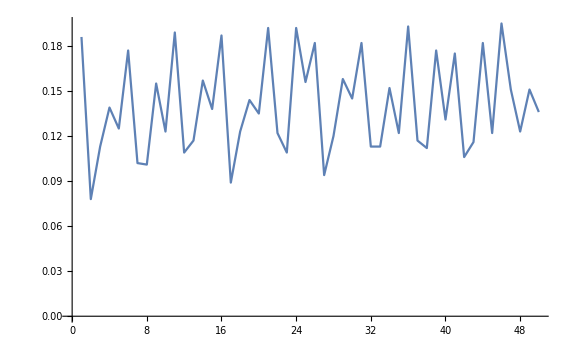

```mathematica
ListLinePlot[timing]
```

```mathematica
mat
```

{{{{0}},{{0}},{{0}},{{0.,0.113006,0.101006,0.117007,0.123007,0.109007,0.120007,0.113007,0.112007,0.116007,0.123007}},{{0}},{{0}},{{0}}},{{{0}},{{0}},{{0}},{{0}},{{0}},{{0}},{{0}}},{{{0}},{{0}},{{0}},{{0}},{{0}},{{0}},{{0}}},{{{0}},{{0}},{{0}},{{0}},{{0.,0.18601,0.177011,0.189011,0.18701,0.192011,0.18201,0.18201,0.193011,0.17501,0.195012}},{{0}},{{0.,0.139008,0.155009,0.157009,0.144009,0.192011,0.158009,0.152009,0.17701,0.18201,0.151009}}},{{{0.,0.0780051,0.102005,0.109006,0.089005,0.122007,0.0940051,0.113006,0.117006,0.106006,0.151008}},{{0}},{{0}},{{0}},{{0}},{{0}},{{0}}},{{{0}},{{0}},{{0}},{{0}},{{0}},{{0}},{{0}}},{{{0}},{{0}},{{0}},{{0.,0.125007,0.123007,0.138008,0.135007,0.156009,0.145009,0.122007,0.131007,0.122007,0.136008}},{{0}},{{0}},{{0}}}}

```mathematica
DE = Flatten@DeleteCases[mat[[4,5]],0.,Infinity]
```

{0.18601,0.177011,0.189011,0.18701,0.192011,0.18201,0.18201,0.193011,0.17501,0.195012}

```mathematica
DeleteCases[mat,0.,Infinity];
```

```mathematica
AD = Flatten@DeleteCases[mat[[1,4]],0.,Infinity]
```

{0.113006,0.101006,0.117007,0.123007,0.109007,0.120007,0.113007,0.112007,0.116007,0.123007}

```mathematica
Fit[AD,A*Exp[(-(x-μ)^2)/(2 σ^2)],x]
```

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Fit[{0.113006,0.101006,0.117007,0.123007,0.109007,0.120007,0.113007,0.112007,0.116007,0.123007},A ⅇ^(-(x-μ)^2/(2 σ^2)),x]

```mathematica
dehist = HistogramList[DE,{0,.8,.01}]
```

{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,5,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
dehist1 = Table[{(dehist[[1]][[x]] + dehist[[1]][[x+1]])/2,dehist[[2]][[x]]},{x,1,Length[dehist[[2]]]}];
```

0.

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8}

```mathematica
DistributionFitTest[dehist]
```

DistributionFitTest::rctnln: The argument {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,«3»,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«31»},{«1»}} at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

DistributionFitTest[{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,5,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]